```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"QBMMlib.wl"];
Get[NotebookDirectory[]<>"TimeSteppers.wl"];
```

```mathematica
(* Input parameters *)
model="nonlinear";
If[model=="linear",
	Ca=1/2;γ=1;Rey=Infinity;
	Cp0=1;
	Cp[t_]:=Cp0;
	Toneperiod=3.4 (1/Cp0)^0.75;
	(*myeqn=rdd+rd+(r-ro)+Cp[t]==0;*)
	myeqn=rdd+rd+(r-ro)==0;
];
If[model=="nonlinear",
	Ca=1/2;(*γ=1;*)
	(*Cp0=0.9;*)
	Cp0=1/0.9;
	Toneperiod=3.4  (1/Cp0)^0.75;
	Cp[t_]:=p(* Cp0*);
	(*Cp[t_]:=If[t<Toneperiod,Cp0 Sin[2 Pi t/Toneperiod]+1,1];*)
	myeqn=r rdd+(3/2)rd^2==(ro/r)^(3 γ)-Cp[ttt];
];

Nperiod=5;
T=Nperiod Toneperiod;

dt=1.  10^-5;dt0=dt;
dtmin=dt;dtmax=10000dt;
tol=12 10^-6;

μRd=10^-14;σRd=Sqrt[0.05];
𝒟v=NormalDistribution[μRd,σRd];	

dimensions=3;
If[dimensions==2,
	nro=1;
	Ros={1};wRos={1};
	myvars={r,rd};
	myidx={i1,i2};
	μR=1.;σR=0.1;
	𝒟r=LogNormalDistribution[Log[μR],σR];
	RRdPDF=ProductDistribution[𝒟r,𝒟v];
	ro=μR;
	momRRd[i_,j_,k_]:=Moment[RRdPDF,{i,j}];
];
If[dimensions==3,
	μRo=1.;σRo=0.1;
	nro=2;
	𝒟ro=LogNormalDistribution[Log[μRo],σRo];
	myvars={r,rd,ro};
	myidx={i1,i2,i3};
	momRo[i_]:=Moment[𝒟ro,i];
	momRos=Table[momRo[i],{i,0,2nro-1}];
	{Ros,wRos}=wheeler[momRos,nro];
	If[Min[Ros]<0,Print["Negative Ro!"];Abort[];];	
	Do[
		μR=Ros[[i]];σR=0.1;
		𝒟r[i]=LogNormalDistribution[Log[μR],σR];
		RRdPDF[i]=ProductDistribution[𝒟r[i],𝒟v];
	,{i,nro}];
	momRRd[i_,j_,k_]:=Moment[RRdPDF[k+1],{i,j}];
	RRdRoPDF=ProductDistribution[𝒟r,𝒟v,𝒟ro];
];

{coefs,exps}=getterms[myeqn,myvars,rdd,myidx];

method="CHyQMOM";(*"CQMOM" or "CHyQMOM"*)
nr=2;
nrd=2;
numperm=2;
If[method=="CHyQMOM"&&nr==3,qmax=0.3];

ks=momidx[nr,nrd,method,numperm,nro];
ksp={{3,0,0},{2,1,0},{3,2,0},{3(1-γ),0,3γ}};
```

Set::shape: Lists {Ros,wRos} and wheeler[{1.,1.00501,1.0202,1.04603},2] are not the same shape.

Part::partd: Part specification Ros⟦1⟧ is longer than depth of object.

Part::partd: Part specification Ros⟦2⟧ is longer than depth of object.

```mathematica
coefs
exps
```

{-i2 p,-(3 i2)/2,i2,i1}

{{-1+i1,-1+i2,i3},{-1+i1,1+i2,i3},{-1+i1-3 γ,-1+i2,i3+3 γ},{-1+i1,1+i2,i3}}

```mathematica
idx={{1,0},{2,0},{1,1},{0,1},{0,2}};
```

```mathematica
nbub=10^-4/(3.141592653589793 4/3);
```

0.0000238732

```mathematica
nbub=(3/(4 Pi)) 10^-4/(1.0000500012500209^3)
```

0.0000238697

```mathematica
0.000023869660746125272
```

```mathematica
nbub Table[Moment[ProductDistribution[LogNormalDistribution[Log[muR],sigR],NormalDistribution[muV,sigV]],i],{i,idx}]/.{sigR->0.01,sigV->0.05,muR->1,muV->0}
```

{0.0000238709,0.0000238744,0.,0.,5.96742×10^-8}

```mathematica
{0.00002387085425900015,0.000023874435155699542,0.,0.,5.967415186531319*^-8}
```

```mathematica
ks
```

{{0,0,0},{1,0,0},{0,1,0},{2,0,0},{1,1,0},{0,2,0}}

```mathematica
(* conditioned on R_o,l moments *)
frhs[mom_,tin_,indx_]:=Module[{rhs,rule,myexps,mycoefs},
	rule=Flatten[{Table[myidx[[i]]->indx[[i]],{i,dimensions}],ttt->tin}];
	myexps=Table[exps[[i]]/.rule,{i,Length[exps]}];
	mycoefs=Table[coefs[[i]]/.rule,{i,Length[coefs]}];
	(* this now multiplies each term by the Ro, +1 added to Ros to promote 0 -> 1 index  *)
	rhs=Sum[
			mycoefs[[i]]pow[Ros[[indx[[3]]+1]],myexps[[i,3]]-indx[[3]]]
			mom[myexps[[i,1]],myexps[[i,2]],1+indx[[3]]]
		,{i,Length[coefs]}];
	Return[rhs,Module];
];

myrhs[moms_,t_]:=Module[{mom,rhs,momout,rhs1,rhs2,momsp1,momsp2,momout1,momout2},
	If[method=="CHyQMOM",
		{w,xix,xiy}=chyqmom[moms,ks,qmax,wRos,Ros];
		{momout,mom}=quad[w,xix,xiy,method,nr,nrd,ks,0,wRos,Ros];
		rhs=Table[frhs[mom,t,ks[[i]]],{i,Length[ks]}];
	];
	If[method=="CQMOM",
		If[numperm==2,
			{w,xi,xis}=cqmom[12,moms,ks,nr,nrd,nro,wRos,Ros];
			{momout1,mom}=quad[w,xi,xis,method,nr,nrd,ks,12,wRos,Ros];
			rhs1=Table[frhs[mom,t,ks[[i]]],{i,Length[ks]}];
		
			{w,xi,xis}=cqmom[21,moms,ks,nr,nrd,nro,wRos,Ros];
			{momout2,mom}=quad[w,xi,xis,method,nr,nrd,ks,21,wRos,Ros];
			rhs2=Table[frhs[mom,t,ks[[i]]],{i,Length[ks]}];

			momout=(momout1+momout2)/2;
			rhs=(rhs1+rhs2)/2;
		,
			{w,xi,xis}=cqmom[12,moms,ks,nr,nrd,nro,wRos,Ros];
			{momout,mom}=quad[w,xi,xis,method,nr,nrd,ks,12,wRos,Ros];
			rhs=Table[frhs[mom,t,ks[[i]]],{i,Length[ks]}];
		];
	];
	Return[{momout,rhs},Module];
];
```

```mathematica
(* ic: conditioned moments for each Subscript[R, o,l] *)
moms=Table[momRRd[ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];

sol={};ts={};dets={};abscissa={};fullmoms={};
t=0;dt=dt0;
Monitor[While[t≤T,
	{moms,mome,e}=RK23[moms,myrhs,t,dt];
	If[method=="CHyQMOM",AppendTo[abscissa,Table[Thread[{xix[j],xiy[j]}],{j,nro}]]];
	If[method=="CQMOM",AppendTo[abscissa,Table[Flatten[Table[Thread[{xis[j][i],xi[j][[i]]}],{i,nrd}],1],{j,nro}]]];
	AppendTo[sol,moms];
	AppendTo[ts,t];

	mominv1[moms_,i_,j_,k_]:=moms[[Position[ks,{i,j,k}][[1,1]]]];

	momtot[i_,j_,k_]:=Sum[wRos[[l+1]]Ros[[l+1]]^k mominv1[moms,i,j,l],{l,0,nro-1}];
	fullmom=Table[momtot[ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];
	momtot[i_,j_,k_]:=Sum[wRos[[l+1]]Ros[[l+1]]^k mominv1[mome,i,j,l],{l,0,nro-1}];
	fullmome=Table[momtot[ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];

	e=Norm[fullmom-fullmome]/Norm[fullmom];
	AppendTo[fullmoms,fullmom];

	t=t+dt;
	dt=dt Min[Max[Sqrt[tol/(2 e)],0.3],2.];
dt=Min[Max[0.9 dt,dtmin],dtmax];

If[Norm[moms]>10^8,Print["Crash ",100 t/T];Break[]];
];
,TableForm[{{"Time",100t/T},{"δt",dt/dt0},{"Moments",Max[Abs[moms]]}}]
]//AbsoluteTiming
Length[ts]
```

Max::nord: Invalid comparison with 0.0000124134+2.21441×10^-19 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

$Aborted

22

```mathematica
myn=100;
plottingfac=1;
myts=Table[ts[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/myn]}];
Do[myabscissa[j]=Table[abscissa[[i,j]],{i,1,Length[abscissa],Floor[Length[abscissa]/N[myn]]}],{j,nro}];
Do[
	xdat[j]=myabscissa[j][[All,All,1]];
	ydat[j]=myabscissa[j][[All,All,2]];
	xmax[j]=If[Max[xdat[j]]>0,1.2 Max[xdat[j]],0.8 Max[xdat[j]]];
	xmin[j]=If[Min[xdat[j]]<0,1.2 Min[xdat[j]],0.8 Min[xdat[j]]];
	ymax[j]=If[Max[ydat[j]]>0,1.2 Max[ydat[j]],0.8 Max[xdat[j]]];
	ymin[j]=If[Min[ydat[j]]<0,1.2Min[ydat[j]],0.8 Min[ydat[j]]];
,{j,nro}];
xminF=Min[Table[xmin[j],{j,nro}]];
xmaxF=Max[Table[xmax[j],{j,nro}]];
yminF=Min[Table[ymin[j],{j,nro}]];
ymaxF=Max[Table[ymax[j],{j,nro}]];

dat3d=Table[Flatten[Table[Table[Flatten[{Ros[[j]],myabscissa[j][[k,i]]},1],{i,Length[myabscissa[j][[k]]]}],{j,nro}],1],{k,Length[myabscissa[1]]}];
```

```mathematica
ListAnimate[ParallelTable[
ListPlot[
	Table[myabscissa[j][[i]],{j,nro}],PlotRange->{{xminF//Re,xmaxF//Re},{yminF//Re,ymaxF//Re}},AxesLabel->{"R","V"}]
,{i,1,Length[myabscissa[1]]/plottingfac}]]
```

```mathematica
anim=ListAnimate[
	ParallelTable[
		ListPointPlot3D[dat3d[[i]],PlotRange->{{0.9Min[Ros],1.1Max[Ros]},{xminF//Re,xmaxF//Re},{yminF//Re,ymaxF//Re}},
			AxesLabel->{"Ro","R","V"}]
	,{i,Length[dat3d]/plottingfac}]
]
(*Export["~/Desktop/anim2.avi",anim,AnimationRunTime->6];*)
```

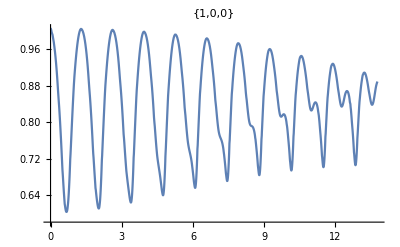
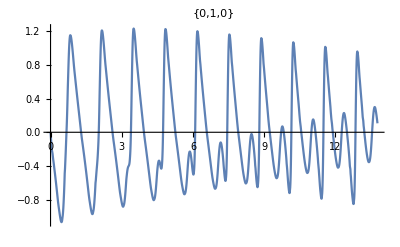
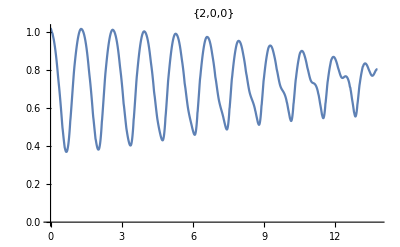
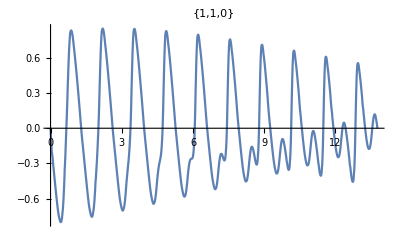
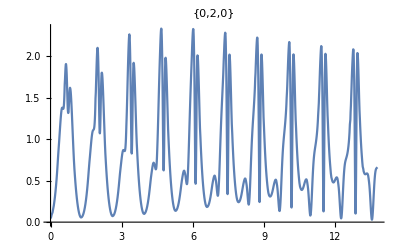

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,fullmoms[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
(* Verify with Monte Carlo *)
If[
	dimensions==3,
	NcasesRRd=50;
	cases=RandomVariate[RRdRoPDF,Ncases];

	NcasesRo=50;
	casesRo=RandomVariate[𝒟ro,NcasesRo]//Sort;
	Do[casesRRd[i]=RandomVariate[ProductDistribution[LogNormalDistribution[Log[casesRo[[i]]],σR],𝒟v],NcasesRRd],{i,NcasesRo}];
	cases=Flatten[Table[{casesRRd[kk][[i,1]],casesRRd[kk][[i,2]],casesRo[[kk]]},{i,NcasesRRd},{kk,NcasesRo}],1];
	Ncases=Length[cases];
,
	Ncases=3000;
	cases=RandomVariate[RRdPDF,Ncases];
	cases=Table[{cases[[i,1]],cases[[i,2]],ro},{i,Ncases}];
];

Clear[t];
If[model=="linear",
	β=2/Rey;ω2= 2 γ Ca;
	myr=ParallelTable[
	r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
If[model=="nonlinear",
	myr=ParallelTable[
r[t]/.(NDSolve[
{r[t]r''[t]+3/2 r'[t]^2 ==(cases[[i,3]]/r[t])^(3 γ)-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
mydr=ParallelTable[D[myr[[i]],t],{i,Ncases}];

Nt=100;ts2=Table[i,{i,0,T,T/Nt}];
ts2=myts;Nt=Length[ts2];
P=Table[
	Table[
	{
	myr[[j]]/.{t->ts2[[i]]},
	mydr[[j]]/.{t->ts2[[i]]},
	cases[[j,3]]
	}
	,{j,Ncases}]
,{i,Nt}];

mcmoms=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;3]]]},{i,Nt}],{j,Length[ks]}];
mcmomssp=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ksp[[j,1;;3]]]},{i,Nt}],{j,Length[ksp]}];
```

```mathematica
plts=ParallelTable[
Show[
DensityHistogram[P[[i]],PlotRange->{{xmin,xmax},{ymin,ymax},All}],
ListPlot[myabscissa[[i]],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]]
,{i,1,Length[P]/1}];
vid=ListAnimate[plts]
```

```mathematica
(*Export["~/Desktop/movie.avi",vid]*)
```

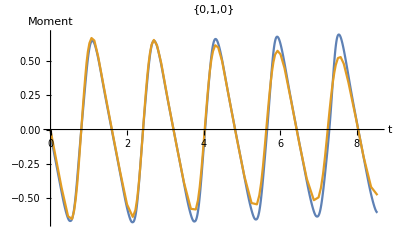
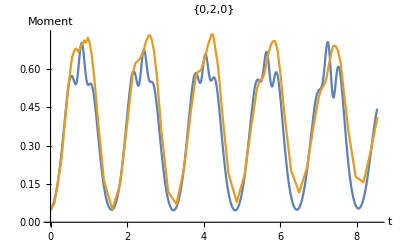
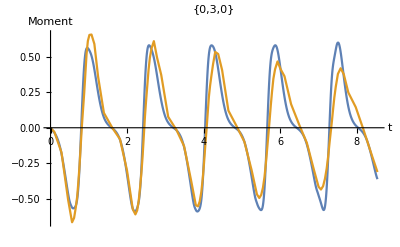
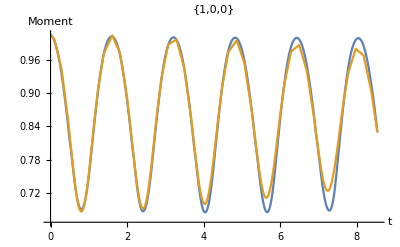
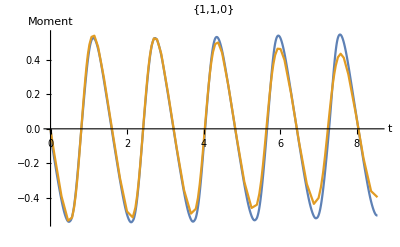
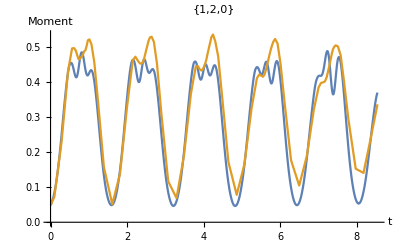
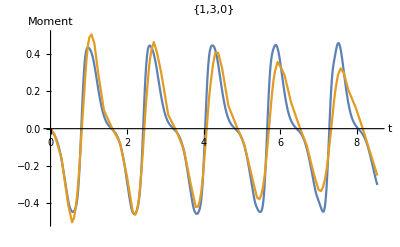
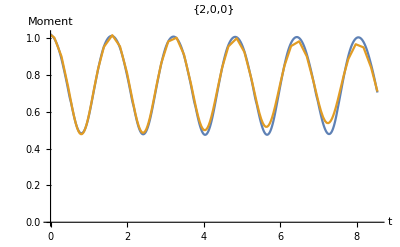

{}

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[{Thread[{ts,fullmoms[[All,i]]}],mcmoms[[i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]],AxesLabel->{"t","Moment"}]]
]
,{i,1,Length[moms]}]
plots

plots={};
Do[
AppendTo[plots,ListPlot[{Thread[{ts,spsol[[All,i]]}],mcmomssp[[i]]},Joined->True,PlotRange->All,PlotLabel->ksp[[i]],AxesLabel->{"t","Moment"}]]
,{i,1,Length[momsp]}]
plots
```